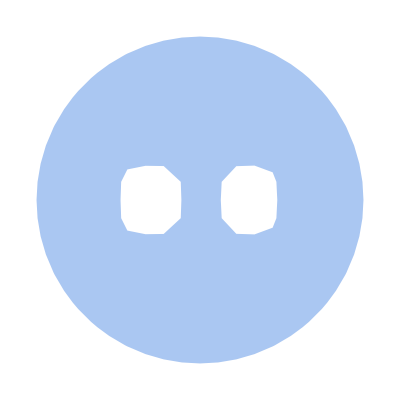

{DirichletCondition[u[x,y]==5,Abs[-1.5+x]^3.5+0.5 Abs[y]^3.5==0.6],DirichletCondition[u[x,y]==-5,0.8 Abs[1.5+x]^4+0.5 Abs[y]^4==0.6],DirichletCondition[u[x,y]==0,x^2+y^2==25]}

{{u→InterpolatingFunction[…]}}

-Graphics-

```mathematica
outerEl=x^2+y^2<=25;
innerEl1=Abs[-1.5+x]^3.5+0.5 Abs[y]^3.5<=0.6;
innerEl2=0.8 Abs[1.5+x]^4+0.5 Abs[y]^4<=0.6;
outerArea=ImplicitRegion[outerEl,{x,y}];
innerArea1=ImplicitRegion[innerEl1,{x,y}];
innerArea2=ImplicitRegion[innerEl2,{x,y}];
fullArea=RegionDifference[RegionDifference[outerArea,innerArea1],innerArea2];
Region[fullArea]
laplaceEquation = Laplacian[u[x,y], {x,y}] == 0;
conditions = {
DirichletCondition[u[x,y]== 5, Abs[-1.5+x]^3.5+0.5 Abs[y]^3.5==0.6],
DirichletCondition[u[x,y]== -5, 0.8 Abs[1.5+x]^4+0.5 Abs[y]^4==0.6],
DirichletCondition[u[x,y]== 0, x^2+y^2 == 25]
}

res = NDSolve[{laplaceEquation, conditions}, u, {x,y} ∈ fullArea]
resPlt = ContourPlot[u[x,y]/. First[res],{x,y}∈fullArea,Contours->20,ColorFunction->"LightTemperatureMap",PlotLegends->Automatic]
```

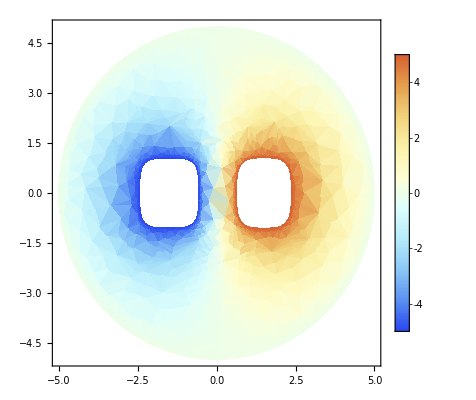

```mathematica
DensityPlot[u[x,y]/. First[res],{x,y}∈fullArea,ColorFunction-> "LightTemperatureMap",PlotLegends->Automatic]
```

```mathematica
contourPlt = ContourPlot[Evaluate[u[x,y]/. res]==2,{x,y}∈fullArea,Contours->{1},PlotLegends->Automatic, ContourStyle->Black];
Show[resPlt, contourPlt]
```

-Graphics-

```mathematica
points=Cases[Normal@contourPlt,Line[pts_]:>pts,Infinity];
pointPairs=Flatten[points,1];
totalDistance = 0;
For[i=1,i<=Length[pointPairs]-1,i++,totalDistance+= EuclideanDistance[pointPairs[[i]], pointPairs[[i+1]]]]
totalDistance
```

12.3867